# KASUS TOV GR constant energy density

## Forward lalu Backward

### Forward calculation

```mathematica
Clear["Global`*"]
```

```mathematica
(* Model densitas energi konstan *)
ϵ[p_]=0p+240.; 
dϵdp=D[ϵ[p],p];
(* Model LinEoS *)
```

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
r0=10^(-3);(* radius di pusat *)
rmax=100000.;
MCC=1 *10^-9; (* Massa di pusat *)
PCC=75; (* Tekanan di pusat *)
```

```mathematica
2GS MCC/r0
```

7.71165×10^6

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solf=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 14251.7}}, <>],p→InterpolatingFunction[{{0.001, 14251.7}}, <>]}

14251.7

14251.714181872905     2.6087447517570204     240.     75

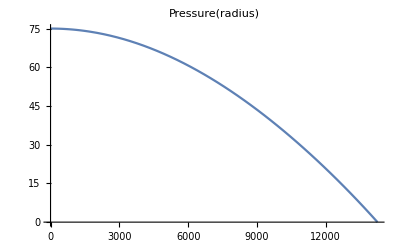

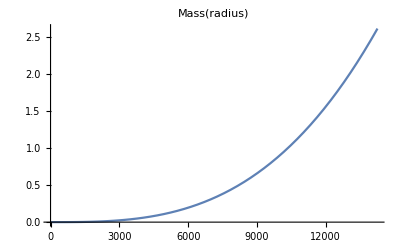

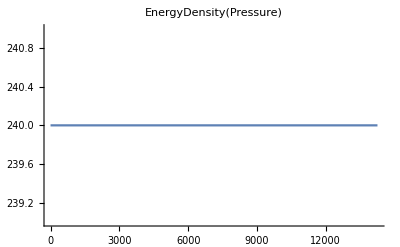

```mathematica
mo[r_]=Evaluate[m[r]/. solf];
po[r_]=Evaluate[p[r]/. solf];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

### Reverse calculation

```mathematica
rmax0=10^(-3);
r00=rStar(* radius di permukaan *)
MCC=mo[rStar]; (* Massa di permukaan *)
MCC/MSS
PCC=po[rStar] (* Tekanan di permukaan *)
2GS MCC/r00
```

14251.7

2.60874

6.10623×10^-15

0.541103

```mathematica
Clear[rStar2];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r00]==MCC , p[r00]==PCC},{m,p},{r,r00,rmax0},Method->{"EventLocator","Event" :>{r},"EventAction":>Throw[rStar2=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax0]
solb=NDSolve`ProcessSolutions[state]
rStar2
```

{m→InterpolatingFunction[{{0.001, 14251.7}}, <>],p→InterpolatingFunction[{{0.001, 14251.7}}, <>]}

rStar2

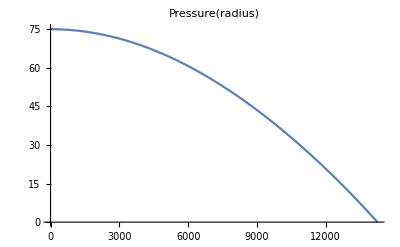

-Graphics-

-Graphics-

```mathematica
moo[r_]=Evaluate[m[r]/. solb];
poo[r_]=Evaluate[p[r]/. solb];
mStar=moo[rStar];
Plot[{poo[r]},{r,rmax0,r00},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{moo[r]/MSS},{r,rmax0,r00},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[poo[r]]},{r,rmax0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

### Perbandingan

```mathematica
(* forward *) 

NumberForm[{r0,mo[r0]/MSS,po[r0]},12]
NumberForm[{rStar,mo[rStar]/MSS,po[rStar]},12]
```

{1/1000,8.96458987001×10^-25,75.}

{14251.7141819,2.60874475176,6.10622663544×10^-15}

```mathematica
(* backward *) 

NumberForm[{rmax0,moo[rmax0]/MSS,poo[rmax0]},12]
NumberForm[{r00,moo[r00]/MSS,poo[r00]},12]
```

{1/1000,7.05515601947×10^-10,75.32905464}

{14251.7141819,2.60874475176,6.10622663544×10^-15}

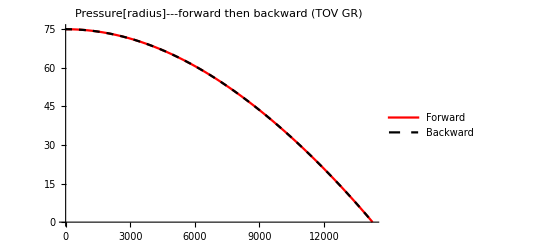

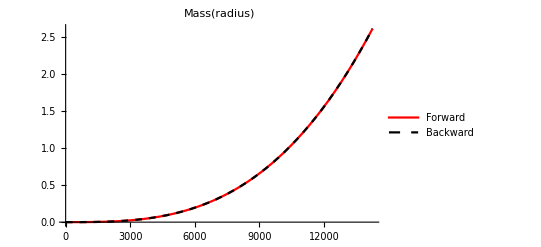

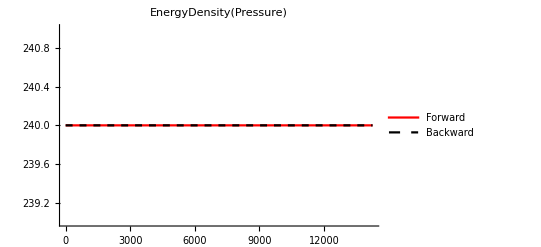

```mathematica
Plot[{po[r],poo[r]},{r,r0,r00},PlotRange->All,PlotLabel->"Pressure[radius]---forward then backward (TOV GR)",PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{mo[r]/MSS,moo[r]/MSS},{r,r0,r00},PlotRange->All,PlotLabel->Mass[radius],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{ϵ[po[r]],ϵ[poo[r]]},{r,r0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
```

```mathematica
NumberForm[2 GS mo[rStar]/rStar,12]
rStar
mo[rStar]/MSS
2GS mo[rStar]
```

0.541102988991

14251.7

2.60874

7711.65